```mathematica
SetDirectory["D:\\airAndWater\\organisms"]
```

D:\airAndWater\organisms

```mathematica
SetDirectory["D:\\grafiliv - stayin alive\\organisms"]
```

D:\grafiliv - stayin alive\organisms

```mathematica
GetOrganism[orgNo_]:=With[{path=StringForm["org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
GenomeSize[orgNo_]:=With[{
g ="genome"/.GetOrganism[orgNo]
},
Length["vertices"/.g]+Length["links"/.g]
]
```

```mathematica
GetParent[orgNo_]:=Module[{path,g,n,s,i},
Quiet[
path = StringForm["org``.json",orgNo];
{g,n,s,i}=Import[path//ToString];
"parent"/.i
]
]
```

```mathematica
oMax=Length[FileNames[]]-1;
δo=Ceiling[oMax/500];
frames=Table[frame,{frame,0,oMax,δo}];
data=ParallelMap[GenomeSize,frames];
```

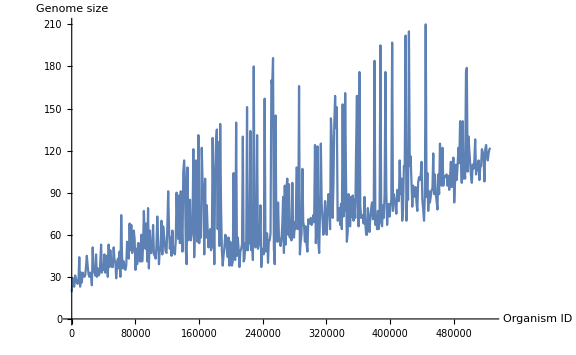

```mathematica
ListLinePlot[data,DataRange->{0,oMax},AxesLabel->{"Organism ID","Genome size"}, ImageSize->Large]
```

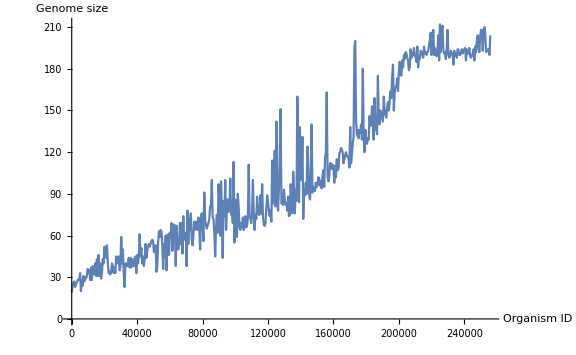

```mathematica
ancestors=NestWhileList[GetParent,oMax,#>0&];
data2=ParallelMap[GenomeSize,ancestors]//Reverse;
```

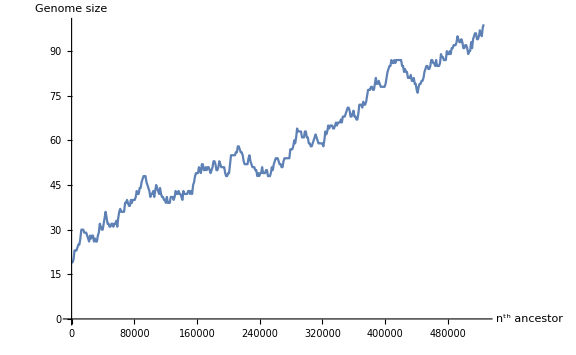

```mathematica
ListLinePlot[data2,DataRange->{0,oMax},AxesLabel->{"n^th ancestor","Genome size"}, ImageSize->Large]
```